# Orthogonal faces of the quantum set in the CHSH scenario

## Preliminaries

We want to study the geometry of the quantum set of behaviors (correlations), which is convex. Specifically, we want to study the quantum set through the dual perspective. Since one can fully characterize a convex set in terms of its extremal points, it will be then sufficient to study orthogonal faces (faces of the dual).

One defines operators acting on the single-qubit space as

```mathematica
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];
I2=IdentityMatrix[2];
```

and operators acting on the 2-qubit space using the tensor product of single-qubit operators as

```mathematica
ZA=KroneckerProduct[Z,I2];
ZB=KroneckerProduct[I2,Z];
XA=KroneckerProduct[X,I2];
XB=KroneckerProduct[I2,X];
ZZ=KroneckerProduct[Z,Z];
XX=KroneckerProduct[X,X];
ZX=KroneckerProduct[Z,X];
XZ=KroneckerProduct[X,Z];
II=KroneckerProduct[I2,I2];
```

### General realization and behavior

Now, one considers the realization given by

```mathematica
phi[θ_]:= {Cos[θ],0,0,Sin[θ]};
$Assumptions=θ∈Reals&&a[0]∈Reals&&a[1]∈Reals&&b[0]∈Reals&&b[1]∈Reals;
A[i_]:=Cos[a[i]]ZA+Sin[a[i]]XA;
B[i_]:=Cos[b[i]]ZB+Sin[b[i]]XB;
```

Such implementation gives the following probability distribution (behavior)

```mathematica
(*Here, A and B are matrices*)
Ops={{II, B[0],B[1]},{A[0],A[0].B[0],A[0].B[1]},{A[1],A[1].B[0],A[1].B[1]}};
Pprime[θ_] := Flatten[
Table[FullSimplify[ConjugateTranspose[phi[θ]].Ops[[i,j]].phi[θ]],{i,1,3},{j,1,3}]
];
P[θ_]:=Drop[Pprime[θ],1];
P[θ]//MatrixForm
```

(Cos[2 θ] Cos[b[0]]
Cos[2 θ] Cos[b[1]]
Cos[2 θ] Cos[a[0]]
Cos[a[0]] Cos[b[0]]+Sin[2 θ] Sin[a[0]] Sin[b[0]]
Cos[a[0]] Cos[b[1]]+Sin[2 θ] Sin[a[0]] Sin[b[1]]
Cos[2 θ] Cos[a[1]]
Cos[a[1]] Cos[b[0]]+Sin[2 θ] Sin[a[1]] Sin[b[0]]
Cos[a[1]] Cos[b[1]]+Sin[2 θ] Sin[a[1]] Sin[b[1]])

The behavior is correct!

## Bell expression and Bell operator

### Background

Characterizing orthogonal faces means to characterize Bell expressions.

All possible Bell expressions for the {n=2, m=2, \Delta=2} scenario can be parametrized by eight real coefficients:

BellExpression[A, B]  =  a[0] A[0] + a[1] A[1] + b[0] B[0] + b[1] B[1] + c[0, 0] A[0] B[0] + c[1, 0] A[1] B[0] + c[0, 1] A[0] B[1] + c[1, 1] A[1] B[1];

Be careful: the a[i], b[i] are not the same that appears in the measurement operators!!
The Bell expression is related to the Bell operator by 

\vec{\beta}.\vec {P} = < \psi | S | \psi >. 

Given a Bell expression and a given realization, we can construct a Bell operator. In this specific case the Bell operator (induced by such a Bell expression and the considered realization, in terms of projectors) is

(*Matrices*)
S = p[1] ZA + p[2] XA + p[3] ZB + p[4] XB + p[5] ZZ + p[6] XX + p[7] ZX + p[8] XZ;

One can write the general Bell expression as a vector 

β := {b[0], b[1], a[0], c[0, 0], c[0, 1], a[1], c[1, 0], c[1, 1]};

### Conditions to restrict the Bell expression (no calculations)

We define a measurement vector of operators \vec {M} .

M := {B[0],  B[1], A[0], A[0].B[0], A[0].B[1], A[1], A[1].B[0], A[1].B[1]}

- |\xi_i> is a vector of space orthogonal to |\phi>
- \vec{T}_i := <\xi_i|\vec{M}|\phi>
- |\phi> is an eigenstate of S with maximum eigenvalue iff \vec{\beta} \cdot \vec{T}_i = 0.

To find conditions on p[i]s, we first need a basis of the orthogonal of \phi[\theta]:

```mathematica
xi[1] =  {-Sin[θ],0,0,Cos[θ]};
xi[2] = {0,1,0,0};
xi[3] = {0, 0, 1, 0};
```

Recall that \vec{P} = <\psi|\vec{M}|\psi>, \vec{\beta} \cdot \vec{P} = <psi|\vec{\beta} \cdot \vec{M} |psi>, and S = \vec{\beta} \cdot \vec{M}.

Then, we compute the vectors \vec{T}_i for every \xi_i and impose \vec{\beta}. \vec{T}_i = 0. This condition comes from the fact that, if the behavior \vec{P} that we want to characterize has to give a maximal quantum value (\beta_Q, a Tsirelson bound), then the state \phi(\theta) must be an eigenstate of the Bell operator of maximum eigenvalue. We have then four more conditions on the parametrization of the Bell operator. The parameter space is then five-d!

### The Nullifiers representation (just checks!)

We started with 8 p[i] parameters. Then, we find 3 conditions given by the orthogonal states to phi[\theta]. Then, knowing that phi[\theta] must be an eigenvector of S with eigenstate 1, and that the other vectors which are orthogonal to phi[\theta] must be annealed by S, we claim that the Bell operator must be of the form:

S = 1 + \sum_{k=1}^5 p_k N_k,

where the N_ks form a basis of nullifiers of \phi[\theta].

A basis of nullifiers for phi(\theta) is given by

```mathematica
Nullifiers={
ZA - ZB,II-ZZ,XZ+ZX-(1-Sin[2θ])/Cos[2θ](XA+XB),(1+Sin[2θ])(XA-XB)-Cos[2θ](XZ-ZX),II-Sin[2θ]XX-Cos[2θ]ZB
};
```

We verify that we are dealing with nullifiers:

```mathematica
Table[Nullifiers[[k]].phi[θ],{k,1,5}]//FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

It works! Achtung: they are not the same as in the cited paper! But they work!

Our analysis shows that conditions \beta.\vec{T}_i = 0 allows to write the Bell operator as

```mathematica
Sred:=II + Sum[p[k]Nullifiers[[k]],{k, 1,5}]
```

Note that the p[i] are different from the ones of the previous expansion of the Bell operator! To verify, we can determine

```mathematica
ConjugateTranspose[phi[θ]].Sred.phi[θ]//FullSimplify
```

1

As it must be!

### The reduced Bell expression

We now want to write the Bell expression related to the reduced Bell operator. We start by expanding Sred, thought as a formal polynomial expression

```mathematica
NullifiersFormal={
ZAA - ZBB,III-ZAA ZBB,XAA ZBB+ZAA XBB-(1-Sin[2θ])/Cos[2θ](XAA+XBB),(1+Sin[2θ])(XAA-XBB)-Cos[2θ](XAA ZBB-ZAA XBB),III-Sin[2θ]XAA XBB-Cos[2θ]ZBB
};
```

```mathematica
(*Formal indeterminates*)
SredFormal:=III + Sum[p[k]NullifiersFormal[[k]],{k, 1,5}]
```

Following Victor, let us write projectors in terms of measurement operators:

```mathematica
Clear[A,B];
projectors = Solve[{A[0]==Cos[a[0]]ZAA+Sin[a[0]]XAA,A[1]==Cos[a[1]]ZAA+Sin[a[1]]XAA,B[0]==Cos[b[0]]ZBB+Sin[b[0]]XBB,B[1]==Cos[b[1]]ZBB+Sin[b[1]]XBB},{XAA,XBB,ZAA,ZBB}][[1]]//FullSimplify
```

{XAA→(-A[1] Cos[a[0]]+A[0] Cos[a[1]]) Csc[a[0]-a[1]],XBB→(-B[1] Cos[b[0]]+B[0] Cos[b[1]]) Csc[b[0]-b[1]],ZAA→Csc[a[0]-a[1]] (A[1] Sin[a[0]]-A[0] Sin[a[1]]),ZBB→Csc[b[0]-b[1]] (B[1] Sin[b[0]]-B[0] Sin[b[1]])}

We substitute everything in the new expression of the Bell operator, SredFormal (which is parametrized in terms of the 5 p[i]s):

```mathematica
Bellexpr=SredFormal/.projectors//FullSimplify;
```

```mathematica
coeffList=Flatten[CoefficientList[Bellexpr,{A[0],A[1],B[0],B[1]}]]//FullSimplify;
```

The ordering used in the coefficientList function is:  
1   1, 
2   B[1], 
3   B[0], 
4   B[0]B[1], 
5   A[1], 
6   A[1]B[1],
7    A[1] B[0], 
8    ???, 
9    A[0], 
10  A[0]B[1], 
11  A[0]B[0], 
12  ???, 
13   A[0] A[1], 
??, ??, ??.

Then, putting the coefficients in the right ordering (B0, B1, A0, A0B0, A0B1, A1, A1B0, A1B1):

```mathematica
β:={coeffList[[3]],coeffList[[2]],coeffList[[9]],coeffList[[11]],coeffList[[10]],coeffList[[5]],coeffList[[7]],coeffList[[6]]}//FullSimplify;
β//MatrixForm
```

(Csc[b[0]-b[1]] ((p[1]+Cos[2 θ] p[5]) Sin[b[1]]-Cos[b[1]] (p[4] (1+Sin[2 θ])+p[3] (Sec[2 θ]-Tan[2 θ])))
Csc[b[0]-b[1]] (-((p[1]+Cos[2 θ] p[5]) Sin[b[0]])+Cos[b[0]] (p[4] (1+Sin[2 θ])+p[3] (Sec[2 θ]-Tan[2 θ])))
Csc[a[0]-a[1]] (-p[1] Sin[a[1]]+Cos[a[1]] (p[4] (1+Sin[2 θ])+p[3] (-Sec[2 θ]+Tan[2 θ])))
-Csc[a[0]-a[1]] Csc[b[0]-b[1]] (Cos[2 θ] p[4] Sin[a[1]-b[1]]+Sin[a[1]] (Cos[b[1]] p[3]+p[2] Sin[b[1]])+Cos[a[1]] (Cos[b[1]] p[5] Sin[2 θ]+p[3] Sin[b[1]]))
Csc[a[0]-a[1]] Csc[b[0]-b[1]] (Cos[2 θ] p[4] Sin[a[1]-b[0]]+Sin[a[1]] (Cos[b[0]] p[3]+p[2] Sin[b[0]])+Cos[a[1]] (Cos[b[0]] p[5] Sin[2 θ]+p[3] Sin[b[0]]))
Csc[a[0]-a[1]] (p[1] Sin[a[0]]-Cos[a[0]] (p[4] (1+Sin[2 θ])+p[3] (-Sec[2 θ]+Tan[2 θ])))
Csc[a[0]-a[1]] Csc[b[0]-b[1]] (Cos[2 θ] p[4] Sin[a[0]-b[1]]+Sin[a[0]] (Cos[b[1]] p[3]+p[2] Sin[b[1]])+Cos[a[0]] (Cos[b[1]] p[5] Sin[2 θ]+p[3] Sin[b[1]]))
-Csc[a[0]-a[1]] Csc[b[0]-b[1]] (Cos[2 θ] p[4] Sin[a[0]-b[0]]+Sin[a[0]] (Cos[b[0]] p[3]+p[2] Sin[b[0]])+Cos[a[0]] (Cos[b[0]] p[5] Sin[2 θ]+p[3] Sin[b[0]])))

From the fact that the general Bell expression does not consider the identity operator, we get the following linear constraint (coefficient of the identity operator in the expansion of the Bell operator in terms of measurement operators):

```mathematica
coeffList[[1]]==0
```

III (1+p[2]+p[5])==0

### Additional linear constraint

Since we want that the realization of interest verify 1 = \beta.P = <\phi|S|\phi>, we have an additional linear constraint! The constraint reads

```mathematica
1 == Transpose[β].P[θ]//FullSimplify
```

1+p[2]+p[5]==0

Up to now, everything is consistent!

## Variational method

### Variational conditions

Now we can use the fact that small variations around the point of interest should not increase the value of the Bell expression: This conditions give a set of two linear equations:

```mathematica
Clear[θ,a,b]
```

```mathematica
D1P[θ_]:=D[P[θ],a[0]];
D2P[θ_]:=D[P[θ],b[0]];
D3P[θ_]:=D[P[θ],a[1]];
D4P[θ_]:=D[P[θ],b[1]];
D5P[θ_]:=D[P[θ],θ];
```

```mathematica
eq1=Transpose[β].D1P[θ]==0;
eq2=Transpose[β].D2P[θ]==0;
eq3=Transpose[β].D3P[θ]==0;
eq4=Transpose[β].D4P[θ]==0;
eq5=Transpose[β].D5P[θ]==0;
```

```mathematica
expr1=eq1[[1]]//FullSimplify
```

1/2 Csc[a[0]-a[1]] (2 Sin[a[0]] (-Cos[a[1]] (p[3]+Cos[2 θ] p[4]) Sin[2 θ]+(Cos[2 θ] p[1]-p[2]) Sin[a[1]])-2 Cos[a[0]] Sin[2 θ] (Cos[a[1]] p[5] Sin[2 θ]+(p[3]+Cos[2 θ] p[4]) Sin[a[1]]))

```mathematica
expr2=eq2[[1]]//FullSimplify
```

1/2 (-Cot[b[0]-b[1]] (p[2]+p[5])+Csc[b[0]-b[1]] (Cos[b[0]+b[1]] (p[2]+Cos[4 θ] p[5])-2 Cos[2 θ] p[1] Sin[b[0]] Sin[b[1]]+(-2 p[3] Sin[2 θ]+p[4] Sin[4 θ]) Sin[b[0]+b[1]]))

```mathematica
expr3=eq3[[1]]//FullSimplify//Expand;
expr4=eq4[[1]]//FullSimplify//Expand;
expr5=eq5[[1]]//Simplify//Factor;
```

Now expressions 1 and 2 are compatible with the ones obtained by Victor!

### Tsirelson point

Focusing on the specific case of the Tsirelson point, the parameters are:

```mathematica
θ=π/4;
a[0]=0;
a[1]=π/2;
b[0]=π/4;
b[1]=-π/4;
```

Hence, the equations reduce to:

```mathematica
{expr1,expr2,expr3,expr4,expr5}
```

{p[3],1/2 (p[2]-p[5]),-p[3],-p[2]/2+p[5]/2,0}

```mathematica
{expr1,expr2}
```

{p[3],1/2 (p[2]-p[5])}

We successfully recover Victor’s equations!!

## Local bounds

### Local polytopes

```mathematica
Clear[θ,a,b];
a[0]=0;
a[1]=π/2;
b[0]=π/4;
b[1]=-π/4;
```

Formally, the set L of local behaviors is defined by the elements of P that can be written in the form

p(ab|xy) = \int_\Lambda \de \lambda p(a|x,\lambda)p(b|y,\lambda).

We can rephrase the local model as follows. Let λ = (a0, a1, b0, b1) define an assignment of outputs a_x and b_y for each of the inputs x=0,1 and y=0,1. Let d_\lambda \in L denote the corresponding deterministic behavior

d_\lambda(ab|xy) = 1 if a=a_x and b=b_y and 0 otherwise

There are k^{2m} = 16 possible output assignments and therefore 16 such local deterministic behaviors. A behavior p is local if and only if it can be written as a convex combination of these deterministic points. Hence, the set L is a polytope. The local deterministic behaviors d_\lambda correspond to the vertices.

Recall: we are working in the space dual to the behavior space (= the space of Bell expressions). In fact, we have a parametrized Bell expression, this time with 4 parameters (instead of 2, as in the Tsirelson case).

```mathematica
OpsL={{1, i,j},{k,i k,j k},{l,i l,j l}};
Lprime[i_,j_,k_,l_] = Table[FullSimplify[OpsL[[a,b]]],{a,1,3},{b,1,3}];
L[i_,j_,k_,l_]:=Drop[Flatten[Lprime[i,j,k,l] ],1];
L[i,j,k,l] //MatrixForm
```

(i
j
k
i k
j k
l
i l
j l)

The convex region of expressions \beta(r0, r1) with a local maximum smaller than 1 is thus given by all points (r0, r1) satisfying \beta.L \eq 1.

```mathematica
p[5]=-1-p[2];
p[3]=-Cos[2 θ] p[4];
p[2]=(Cos[4 θ] -Cos[2 θ] p[1])/(1-Cos[4θ]);
```

```mathematica
ineqs:=Flatten[Table[Transpose[β].L[i,j,k,l]<=1,{i,{-1,1}},{j,{-1,1}},{k,{-1,1}},{l,{-1,1}}]];
```

We can consider different realizations, in order to reduce the number of parameters!

```mathematica
Table[RegionPlot[Evaluate[And@@ineqs],{p[1],-0.5,0.5},{p[4],-0.5,0.5},
PlotStyle->Directive[Opacity[0.5],Blue],
PlotLabel->Style["Local polytope",Bold,16]],{θ, π/8+π/64, π/4, π/64}]
```

$Aborted

We notice the presence of a symmetry (p[4] -> - p[4]), probably due to the form of the Bell expression.

Let us see what is the form of the Bell expression parametrized by p[1] and p[4]:

```mathematica
β //MatrixForm
```

((Csc[2 θ]^2 (2 Cos[2 θ]+(-3+Cos[4 θ]) p[1]-8 p[4] Sin[2 θ]^3))/(4 √2)
(-Csc[θ]^2 (-1+p[1])-4 p[1]-(1+p[1]) Sec[θ]^2+32 Cos[θ] p[4] Sin[θ])/(8 √2)
p[1]
-(Csc[2 θ]^2 (Cos[4 θ]-Cos[2 θ] p[1]))/(2 √2)
-(Csc[2 θ]^2 (Cos[4 θ]-Cos[2 θ] p[1]))/(2 √2)
2 p[4]
-(Csc[2 θ] (-1+Cos[2 θ] p[1]+2 p[4] Sin[4 θ]))/(2 √2)
(Csc[2 θ] (-1+Cos[2 θ] p[1]-2 p[4] Sin[4 θ]))/(2 √2))

We can define a Measurement vector operator

```mathematica
M := {B[0],B[1],A[0],A[0].B[0], A[0].B[1],A[1],A[1].B[0],A[1].B[1]}
```

The parametrized Bell expression than reads

```mathematica
Collect[Simplify[Transpose[β].M],{p[1],p[4]}]
```

1/16 p[1] (16 A[0]-4 √2 B[1]-√2 B[1] Csc[θ]^2+2 √2 B[0] (-3+Cos[4 θ]) Csc[2 θ]^2+4 √2 Cot[2 θ] Csc[2 θ] A[0].B[0]+4 √2 Cot[2 θ] Csc[2 θ] A[0].B[1]-4 √2 Cot[2 θ] A[1].B[0]+4 √2 Cot[2 θ] A[1].B[1]-√2 B[1] Sec[θ]^2)+1/16 (√2 B[1] Csc[θ]^2+4 √2 B[0] Cot[2 θ] Csc[2 θ]-4 √2 Cos[4 θ] Csc[2 θ]^2 A[0].B[0]-4 √2 Cos[4 θ] Csc[2 θ]^2 A[0].B[1]+4 √2 Csc[2 θ] A[1].B[0]-4 √2 Csc[2 θ] A[1].B[1]-√2 B[1] Sec[θ]^2)+1/16 p[4] (32 A[1]+32 √2 B[1] Cos[θ] Sin[θ]-16 √2 B[0] Sin[2 θ]-8 √2 Csc[2 θ] A[1].B[0] Sin[4 θ]-8 √2 Csc[2 θ] A[1].B[1] Sin[4 θ])

```mathematica
Transpose[β].M //FullSimplify
```

1/16 (4 (√2 (B[0]+B[1]) Cot[2 θ] Csc[2 θ]+4 A[0] p[1]+8 A[1] p[4])+1/(√2)Csc[θ]^2 Sec[θ]^2 ((B[0]+B[1]) (-3+Cos[4 θ]) p[1]-2 A[0].B[0] (Cos[4 θ]-Cos[2 θ] p[1])-2 A[0].B[1] (Cos[4 θ]-Cos[2 θ] p[1])+2 Sin[2 θ] (4 (-B[0]+B[1]) p[4] Sin[2 θ]^2+A[1].B[1] (-1+Cos[2 θ] p[1]-2 p[4] Sin[4 θ])-A[1].B[0] (-1+Cos[2 θ] p[1]+2 p[4] Sin[4 θ]))))

From this form, we should be able to identify the symmetry!

### Vertices as functions of \theta

We have now inequalities parametrized by \theta. To characterize the solution as a function of \theta, it is sufficient to know the vertices, since the solution of the system of inequalities is given by the Convex Hull of the vertices, since we know that the local set L is a polytope! To find the vertices, it is sufficient to find all the intersections between the lines, that are characterized by the equations associated to the inequalities we have.

```mathematica
eqns:=ineqs/.LessEqual->Equal//FullSimplify;
```

We get all unique pairs of equations:

```mathematica
eqnPairs=Subsets[eqns,{2}];
```

We have 16 equations, so the possibilities are

```mathematica
Binomial[16,2]
```

120

Let’s check that everything works:

```mathematica
Length[eqnPairs]
```

120

We now try to solve the equations and find all the “candidate” for the vertices of the local polytopes

```mathematica
rawVertices=DeleteDuplicates[Select[Flatten[Table[Solve[pair,{p[1],p[4]},Reals],{pair,eqnPairs}],1],FreeQ[#,C[1]]&]]
```

We cannot display vertices, as they are functions of \theta. There are 120 pairs of linear equations in p[1] and p[4], so we expect 120 solutions! Everything is working!

But the convex polytope is determined by very few points. How to exclude non-relevant solutions? Let’s try a different approach. We  guess that (maybe!) the vertices are always described by intersections of the same lines! Then, for a fixed \theta, we can try to identify the correct sequence of lines that describe the vertices.

### What can we learn from the Tsirelson point case

Which lines describe the vertices of the local polytope? For the Tsirelson behavior, the local polytope is given by

```mathematica
ineqsEval=ineqs/. θ->π/4;
(*Label each inequality so we can track where vertices come from*)
labeledIneqs=MapIndexed[#1->First[#2]&,ineqsEval];
(*Build all pairs of inequalities and their labels*)
labeledPairs=Subsets[labeledIneqs,{2}];
(*Go through each pair,solve,and check if solution lies in region*)
vertexData=Reap[Do[Module[{pair,eqs,sol},pair=pairEntry[[All,1]];
eqs=pair/. LessEqual->Equal;
sol=Quiet@Solve[eqs,{p[1],p[4]},Reals];
If[Length[sol]>0&&FreeQ[sol[[1]],C[1]]&&And@@(ineqsEval/. sol[[1]]),Sow[{pairEntry[[All,2]],sol[[1]]}]]],{pairEntry,labeledPairs}]][[2,1]];
```

```mathematica
vertexData//Table
```

{{{1,12},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))}},{{1,15},{p[1]→0,p[4]→1/4 (-2+√2)}},{{2,7},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))}},{{2,16},{p[1]→0,p[4]→1/4 (2-√2)}},{{5,10},{p[1]→-(-4+3 √2)/(2 (-1+√2)),p[4]→0}},{{5,16},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))}},{{7,12},{p[1]→-(4-3 √2)/(2 (-1+√2)),p[4]→0}},{{10,15},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))}}}

So, we got the list of lines describing the vertices! Then, we extract the data:

```mathematica
vertexCoords=vertexData[[All,2]];
contributingPairs=vertexData[[All,1]];
```

The couples of lines whose intersections describe the vertices of the dual local polytope for the Tsirelson behavior are

```mathematica
contributingPairs
```

{{1,12},{1,15},{2,7},{2,16},{5,10},{5,16},{7,12},{10,15}}

```mathematica
vertexCoords
```

{{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))},{p[1]→0,p[4]→1/4 (-2+√2)},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))},{p[1]→0,p[4]→1/4 (2-√2)},{p[1]→-(-4+3 √2)/(2 (-1+√2)),p[4]→0},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))},{p[1]→-(4-3 √2)/(2 (-1+√2)),p[4]→0},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))}}

Now, consider the equations corresponding to these couples of lines in the partially entangled case. We can then recover some reasonable candidates for the vertices of the local polytopes in the general case:

```mathematica
vertexDataTheta = Table[Module[{eq1,eq2,sol},eq1=ineqs[[pair[[1]]]]/. LessEqual->Equal;
eq2=ineqs[[pair[[2]]]]/. LessEqual->Equal;
sol=Quiet@Solve[{eq1,eq2},{p[1],p[4]}];
pair->sol],{pair,contributingPairs}];
```

We then store the coordinates of this candidate in a vector v

```mathematica
v =Table[{p[1],p[4]}/.vertexDataTheta[[i,2, 1]],{i, 1, 8}];
```

For the Tsirelson point, we recover the known vertices:

```mathematica
v/.{θ->π/4}//FullSimplify
```

{{-1/2+1/(√2),1/4 (1-√2)},{0,1/4 (-2+√2)},{-1/2+1/(√2),1/4 (-1+√2)},{0,1/4 (2-√2)},{-1+1/(√2),0},{1/2-1/(√2),1/4 (-1+√2)},{1-1/(√2),0},{1/2-1/(√2),1/4 (1-√2)}}

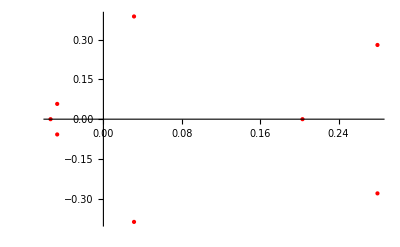
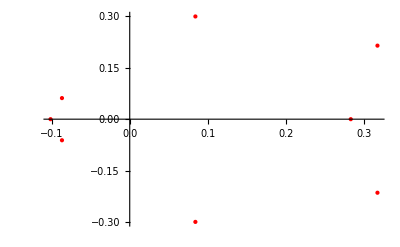
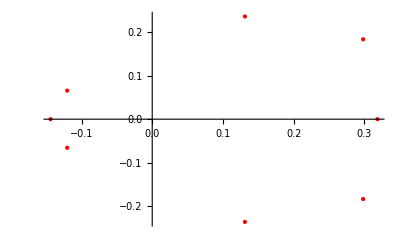
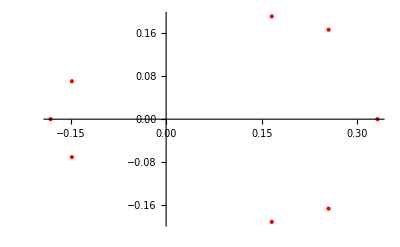
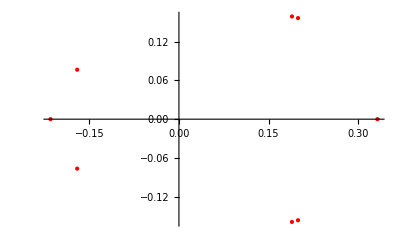
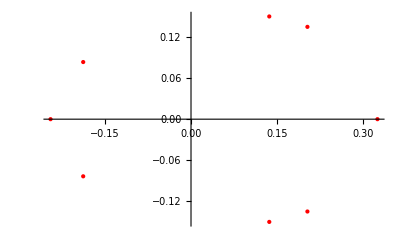
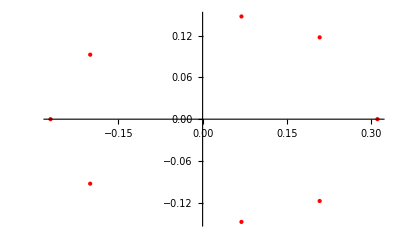
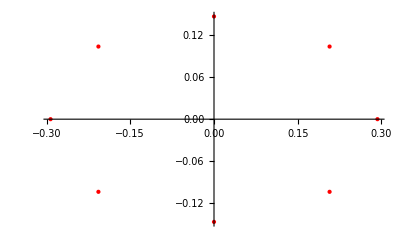

```mathematica
Table[ListPlot[v, PlotStyle->{Red,PointSize[Medium]}],{θ, π/8+π/64, π/4, π/64}]
```

Putting everything together, we verify if the considered points are good candidates for vertices:

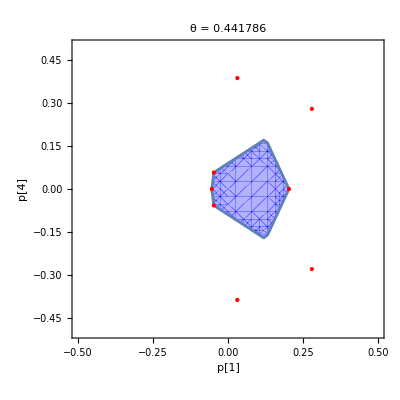
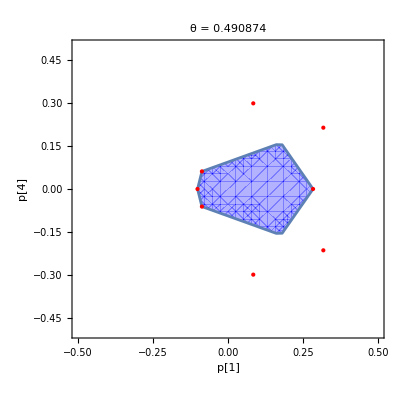
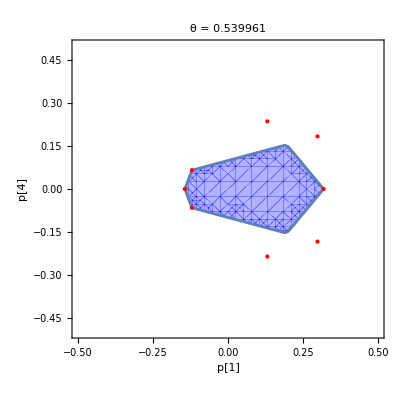
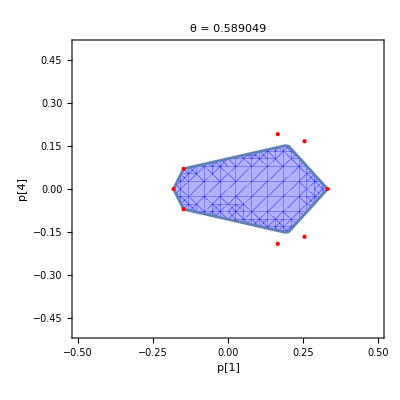
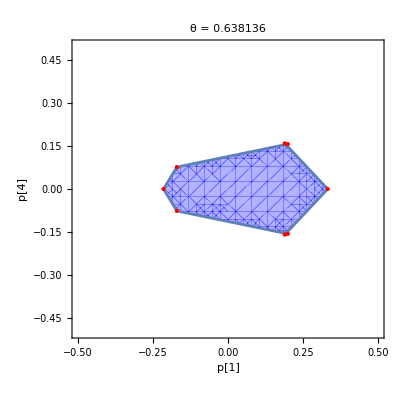
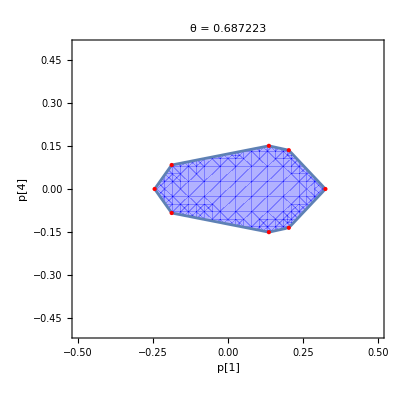
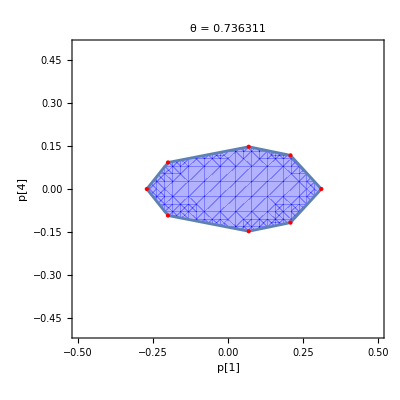
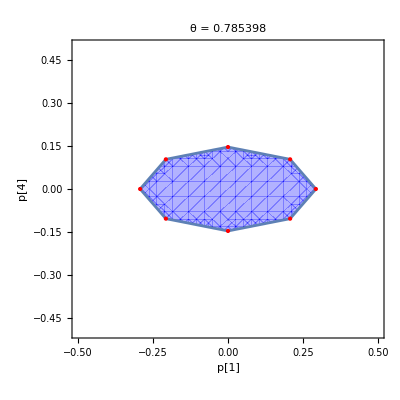

```mathematica
Table[Module[{region,vertexPlot},region=RegionPlot[Evaluate[And@@ineqs/. θ->th],{p[1],-0.5,0.5},{p[4],-0.5,0.5},PlotStyle->Directive[Opacity[0.3],Blue],AxesLabel->{Style["p[1]",Bold,14],Style["p[4]",Bold,14]},PlotLabel->Style["θ = "<>ToString[N[th]],Bold,16]];
vertexPlot=ListPlot[v/. θ->th,(*assuming v is a list of {p[1],p[4]} functions of θ*)PlotStyle->{Red,PointSize[Medium]},PlotRange->All];
Show[region,vertexPlot]],{th,π/8+π/64,π/4,π/64}]
```

We can visualize the evolutions of these eight vertices:

```mathematica
Manipulate[ListPlot[v/. θ->th,PlotStyle->{Red,PointSize[Large]},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"p[1]","p[4]"},PlotLabel->Style["Vertices for θ = "<>ToString[N[th,2]],Bold,14],AspectRatio->1],{{th,π/8,"θ"},π/8+π/64,π/4}]
```

ListPlot::lpn: v is not a list of numbers or pairs of numbers.

Since our candidates are not always the vertices, we store all the 120 parametrized points in a vector:

```mathematica
coordFuncs=({p[1],p[4]}/. #)&/@rawVertices;
```

### Understanding different regimes

Let us try to study the situations in more details:

```mathematica
thetaList=Range[π/8+π/64,π/4,π/2^10];

frames=Table[Module[{region,vertexPlot},region=RegionPlot[Evaluate[And@@(ineqs/. θ->th)],{p[1],-0.5,0.5},{p[4],-0.5,0.5},PlotStyle->Directive[Opacity[0.3],Blue],AxesLabel->{Style["p₁",Bold,14],Style["p₄",Bold,14]},PlotLabel->Style["θ = "<>ToString[N[th]],Bold,16]];
vertexPlot=ListPlot[v/. θ->th,PlotStyle->{Red,PointSize[Medium]},PlotRange->All];
Show[region,vertexPlot]],{th,thetaList}];
```

```mathematica
Manipulate[Column[{frames[[i]],Row[{"θ = ",N[thetaList[[i]]]}]}],{{i,1,"Frame"},1,Length[frames],1}]
```

Part::partd: Part specification frames⟦70⟧ is longer than depth of object.

Part::partd: Part specification thetaList⟦70⟧ is longer than depth of object.

Part::partd: Part specification frames⟦70⟧ is longer than depth of object.

Part::partd: Part specification thetaList⟦70⟧ is longer than depth of object.

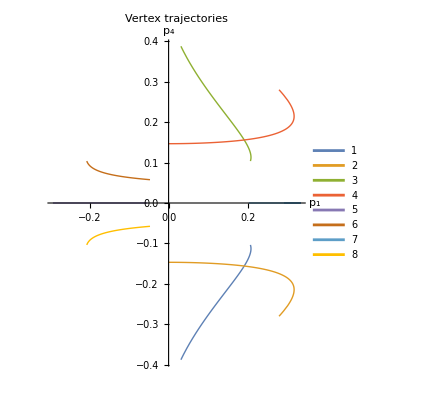

```mathematica
ParametricPlot[Evaluate[Table[v[[i]],{i,1,Length[v]}]/. θ->t],{t,π/8+π/64,π/4},PlotRange->All,AxesLabel->{Style["p₁",Bold,14],Style["p₄",Bold,14]},PlotLegends->Automatic,PlotStyle->Thick,PlotLabel->Style["Vertex trajectories",Bold,16]]
```

Now, we know that vertices 1, 2, 3, 4, do not work in all the regimes. But we need to individuate the missing vertices. To find new candidates, we consider the following:

```mathematica
ineqsN:=Flatten[Table[Transpose[β].L[i,j,k,l]<=1.001,{i,{-1,1}},{j,{-1,1}},{k,{-1,1}},{l,{-1,1}}]];
```

```mathematica
pointsAtTheta[θval_?NumericQ]:=(#/. θ->θval)&/@coordFuncs
```

```mathematica
verticesAtTheta[θval_?NumericQ]:=Module[{allPoints,ineqsEval},ineqsEval=ineqsN/. θ->θval;
allPoints=pointsAtTheta[θval];
Select[allPoints,Function[{pt},And@@Chop@N[ineqsEval/. {p[1]->pt[[1]],p[4]->pt[[2]]}]]]];
```

```mathematica
verticesAtTheta[π/8+π/16]//N
```

{{-0.181479,0.},{-0.14796,0.0706813},{0.331821,0.},{0.198912,0.153281},{-0.14796,-0.0706813},{0.198912,-0.153281}}

As the Manipulate Plot suggests, it seems like there are two regimes: the octagon regime and the hexagon regime. Now, we want to find the angle for which the regime change (which is probably the angle for which points 3 and 4 merge) and the missing vertices.

```mathematica
mergeq=v[[3,2]]==v[[4,2]]//FullSimplify
```

2 Cos[θ] Sin[θ]^2 (((6-4 √2) Cos[θ])/(-3+2 √2+Cos[4 θ])+(-4+3 √2+(-2+√2) Cot[θ])/(-3 √2 Cos[θ]+√2 Cos[5 θ]-3 (-2+√2) Sin[θ]+2 Sin[3 θ]+√2 Sin[5 θ]))==0

```mathematica
FindInstance[mergeq&&θ∈Interval[{π/8+π/64,π/4}],θ,Reals]
```

{{θ→{2 ArcTan[Root0.334Root[1+12 #1-2 #1^2-156 #1^3-17 #1^4+344 #1^5-28 #1^6-344 #1^7-17 #1^8+156 #1^9-2 #1^10-12 #1^11+#1^12&,5]0.3339103357243436]}}}

This is the angle that discriminates between the two regimes.

```mathematica
θT = 0.644539533
```

0.64454

### Vertices

Finally, we want to find the missing vertices: we can use the same method used for the

```mathematica
ineqsEval2=ineqs/. θ->0.589;

(*Label each inequality so we can track where vertices come from*)
labeledIneqs2=MapIndexed[#1->First[#2]&,ineqsEval2];

(*Build all pairs of inequalities and their labels*)
labeledPairs2=Subsets[labeledIneqs2,{2}];

(*Go through each pair,solve,and check if solution lies in region*)
vertexData2=Reap[Do[Module[{pair,eqs,sol},pair=pairEntry[[All,1]];
eqs=pair/. LessEqual->Equal;
sol=Quiet@Solve[eqs,{p[1],p[4]},Reals];
If[Length[sol]>0&&FreeQ[sol[[1]],C[1]]&&And@@(ineqsEval2/. sol[[1]]),Sow[{pairEntry[[All,2]],sol[[1]]}]]],{pairEntry,labeledPairs2}]][[2,1]];
```

```mathematica
vertexData2
```

{{{5,10},{p[1]→-0.181444,p[4]→-5.57726×10^-18}},{{5,16},{p[1]→-0.147935,p[4]→0.0706759}},{{7,12},{p[1]→0.331816,p[4]→-2.60506×10^-16}},{{7,16},{p[1]→0.198915,p[4]→0.153281}},{{10,15},{p[1]→-0.147935,p[4]→-0.0706759}},{{12,15},{p[1]→0.198915,p[4]→-0.153281}}}

We obtained six vertices! It seems it worked! Now, comparing with the other regime,

```mathematica
vertexData
```

{{{1,12},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))}},{{1,15},{p[1]→0,p[4]→1/4 (-2+√2)}},{{2,7},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))}},{{2,16},{p[1]→0,p[4]→1/4 (2-√2)}},{{5,10},{p[1]→-(-4+3 √2)/(2 (-1+√2)),p[4]→0}},{{5,16},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))}},{{7,12},{p[1]→-(4-3 √2)/(2 (-1+√2)),p[4]→0}},{{10,15},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))}}}

The missing vertices is given by the couple  {7, 16} and {12, 15}! We store the vertices in the new regime in a vector:

```mathematica
vertexCoords2=vertexData2[[All,2]];
contributingPairs2=vertexData2[[All,1]];
```

```mathematica
contributingPairs2
```

{{5,10},{5,16},{7,12},{7,16},{10,15},{12,15}}

```mathematica
vertexsols2 = Table[Module[{eq1,eq2,sol},eq1=ineqs[[pair[[1]]]]/. LessEqual->Equal;
eq2=ineqs[[pair[[2]]]]/. LessEqual->Equal;
sol=Quiet@Solve[{eq1,eq2},{p[1],p[4]}];
pair->sol],{pair,contributingPairs2}];
```

```mathematica
v2 =Table[{p[1],p[4]}/.vertexsols2[[i,2, 1]],{i, 1, 6}];
```

Basically, we are done! To verify that we are in the right direction, we plot the graphs for the new regime!

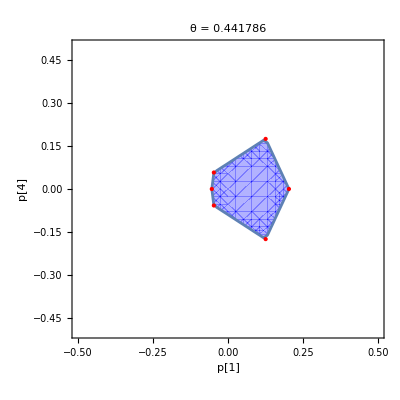
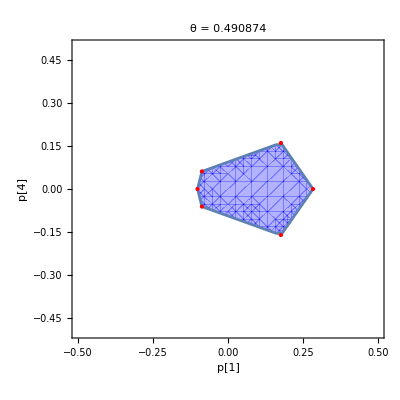
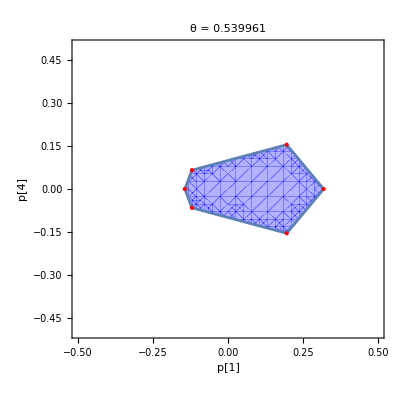
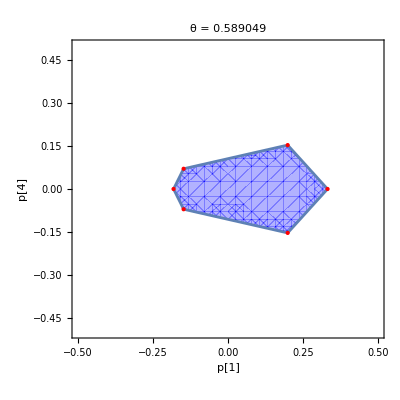
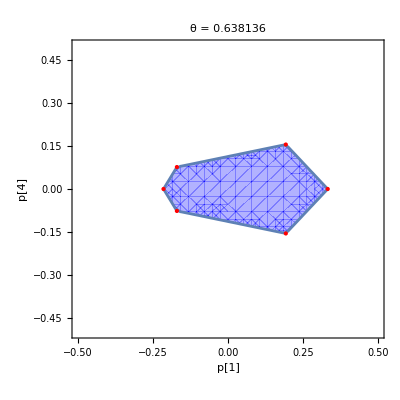
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
frames2 = Table[Module[{region,vertexPlot,verts},
(*Choose the correct vertex list based on theta*)
verts=If[th>θT,v,v2];
(*Plot the region*)region=RegionPlot[Evaluate[And@@ineqs/. θ->th],{p[1],-0.5,0.5},{p[4],-0.5,0.5},PlotStyle->Directive[Opacity[0.3],Blue],AxesLabel->{Style["p[1]",Bold,14],Style["p[4]",Bold,14]},PlotLabel->Style["θ = "<>ToString[N[th]],Bold,16]];
(*Plot the vertices*)vertexPlot=ListPlot[verts/. θ->th,PlotStyle->{Red,PointSize[Medium]},PlotRange->All];
Show[region,vertexPlot]],{th,π/8+π/64,π/4,π/64}]
```

```mathematica
Export["/Users/andrea/Desktop/Local_Polytopes.png",GraphicsGrid[Partition[frames2,4]]]
```

/Users/andrea/Desktop/Local_Polytopes.png

Finally, we want to extract the coordinates of the vertices for every considered value of theta.

```mathematica
vertexCoordsPerTheta=Table[Module[{verts},(*Choose the correct vertex list based on theta*)verts=If[th>θT,v,v2];
(*Evaluate the vertex list with the current theta*)verts/. θ->th],{th,π/8+π/64,π/4,π/64}];
```

```mathematica
vertexCoordsPerTheta[[1]]//N
```

{{-0.0539489,-3.62453×10^-15},{-0.0471597,0.0575582},{0.203139,0.},{0.125475,0.174863},{-0.0471597,-0.0575582},{0.125475,-0.174863}}

Maybe this format is also useful:

```mathematica
vertexCoordsWithTheta=N[Table[Module[{verts,currentVerts},verts=If[th>θT,v,v2];
currentVerts=verts/. θ->th;
{N[th],currentVerts}],{th,π/8+π/64,π/4,π/64}]];
```

```mathematica
vertexCoordsWithTheta
```

{{0.441786,{{-0.0539489,-3.62453×10^-15},{-0.0471597,0.0575582},{0.203139,0.},{0.125475,0.174863},{-0.0471597,-0.0575582},{0.125475,-0.174863}}},{0.490874,{{-0.101577,-3.79164×10^-15},{-0.08692,0.0613573},{0.283531,3.52784×10^-15},{0.176392,0.160678},{-0.08692,-0.0613573},{0.176392,-0.160678}}},{0.539961,{{-0.143851,-1.40978×10^-15},{-0.120287,0.0656677},{0.318659,4.54249×10^-15},{0.195746,0.154632},{-0.120287,-0.0656677},{0.195746,-0.154632}}},{0.589049,{{-0.181479,0.},{-0.14796,0.0706813},{0.331821,1.78249×10^-15},{0.198912,0.153281},{-0.14796,-0.0706813},{0.198912,-0.153281}}},{0.638136,{{-0.214966,6.70581×10^-16},{-0.170381,0.0766283},{0.332368,-6.4801×10^-16},{0.192741,0.15521},{-0.170381,-0.0766283},{0.192741,-0.15521}}},{0.687223,{{0.20273,-0.135418},{0.136305,-0.150662},{0.20273,0.135418},{0.136305,0.150662},{-0.244632,3.1251×10^-16},{-0.187761,0.0838025},{0.324712,1.03702×10^-16},{-0.187761,-0.0838025}}},{0.736311,{{0.20828,-0.117448},{0.0691103,-0.147458},{0.20828,0.117448},{0.0691103,0.147458},{-0.270624,0.},{-0.200089,0.0925966},{0.311141,4.45039×10^-17},{-0.200089,-0.0925966}}},{0.785398,{{0.207107,-0.103553},{0.,-0.146447},{0.207107,0.103553},{0.,0.146447},{-0.292893,0.},{-0.207107,0.103553},{0.292893,0.},{-0.207107,-0.103553}}}}

```mathematica
Export["/Users/andrea/Desktop/vertexCoords.json",vertexCoordsWithTheta]
```

/Users/andrea/Desktop/vertexCoords.json

## Quantum bounds

We now want to find quantum bounds for the Bell expression. We may start implementing the NPA hierarchy with Python and try to see if the behavior is the same as in the Tsirelson’s case!

### Changing notation

```mathematica
Mprime := {B[0],B[1],A[0],A[0]B[0], A[0]B[1],A[1],A[1]B[0],A[1]B[1]};
reducedBell[A_,B_]=Collect[Simplify[Transpose[β].Mprime ],{p[1],p[4]}];
```

Introduced the notation used for the Python package,

```mathematica
AA[i_]:= 2A[0,i]-1;
BB[i_]:=2B[0,i]-1;
```

```mathematica
reducedexpr=Collect[FullSimplify[reducedBell[AA,BB]],{p[1],p[4]}]
```

1/4 p[4] (4 (-2+4 A[0,1])-8 √2 (-1+2 A[0,1]) (-1+B[0,0]+B[0,1]) Cos[2 θ]+8 √2 (-B[0,0]+B[0,1]) Sin[2 θ])+1/4 (4 √2-8 √2 A[0,0]-4 √2 B[0,0]+8 √2 A[0,0] B[0,0]-4 √2 B[0,1]+8 √2 A[0,0] B[0,1]+√2 (-1+2 A[0,1]) (B[0,0]-B[0,1]) Cot[θ]-√2 (-1+A[0,0]) (-1+B[0,0]+B[0,1]) Csc[θ]^2-√2 A[0,0] (-1+B[0,0]+B[0,1]) Sec[θ]^2+√2 (-1+2 A[0,1]) (B[0,0]-B[0,1]) Tan[θ])+1/4 p[1] (2 (-2+√2)+8 A[0,0]-2 √2 B[0,0]-2 √2 B[0,1]-√2 (-1+2 A[0,1]) (B[0,0]-B[0,1]) Cot[θ]+√2 (-1+A[0,0]) (-1+B[0,0]+B[0,1]) Csc[θ]^2-√2 A[0,0] (-1+B[0,0]+B[0,1]) Sec[θ]^2+√2 (-1+2 A[0,1]) (B[0,0]-B[0,1]) Tan[θ])

## SOS Decomposition

We now want to find an SOS decomposition for some of the vertices of the local/quantum dual polytope. First, we look at vertices 5 and 7, since for these vertices p[4] = 0, and the Bell expression is way easier. We already have an ansatz for an SOS decomposition, since we know at least that in the \theta = \pi/4 case, we have the SOS decomposition that Victor found.

```mathematica
Transpose[β].M /.p[4]->0//Simplify
```

1/16 (16 A[0] p[1]-4 √2 Csc[2 θ]^2 A[0].B[0] (Cos[4 θ]-Cos[2 θ] p[1])-4 √2 Csc[2 θ]^2 A[0].B[1] (Cos[4 θ]-Cos[2 θ] p[1])-4 √2 Csc[2 θ] A[1].B[0] (-1+Cos[2 θ] p[1])+4 √2 Csc[2 θ] A[1].B[1] (-1+Cos[2 θ] p[1])+2 √2 B[0] Csc[2 θ]^2 (2 Cos[2 θ]+(-3+Cos[4 θ]) p[1])+(B[1] Csc[θ]^2 (2 Cos[2 θ]+(-3+Cos[4 θ]) p[1]) Sec[θ]^2)/(√2))

### Interesting vertex

The interesting vertex, that can be already reached with the local level 1 of the hierarchy is the 7th

```mathematica
v[[7]]//FullSimplify
```

{(2 √2+√2 Csc[2 θ]^2-2 Csc[θ] Sec[θ])/(2 √2+Cot[2 θ] (-2+√2 Csc[2 θ])-Csc[θ] Sec[θ]),0}

```mathematica
v[[7]]/.θ->π/4
```

{1/2 (2-√2),0}

The remaining vertices (for the first regime are given by:

```mathematica
v//FullSimplify
```

{{(2 (Cos[2 θ]-Sin[2 θ]) ((1-2 √2) Cos[θ]+(-1+√2) Cos[3 θ]-(-3+√2) Sin[θ]+Sin[3 θ]))/(-3 √2 Cos[θ]+√2 Cos[5 θ]-3 (-2+√2) Sin[θ]+2 Sin[3 θ]+√2 Sin[5 θ]),-(2 Cos[θ] (-4+3 √2+(-2+√2) Cot[θ]) Sin[θ]^2)/(-3 √2 Cos[θ]+√2 Cos[5 θ]-3 (-2+√2) Sin[θ]+2 Sin[3 θ]+√2 Sin[5 θ])},{-((-2+√2) (Cos[2 θ]+Cos[6 θ]))/(4-3 √2+√2 Cos[4 θ]),((3-2 √2) Sin[2 θ]^2)/(-3+2 √2+Cos[4 θ])},{(2 (Cos[2 θ]-Sin[2 θ]) ((1-2 √2) Cos[θ]+(-1+√2) Cos[3 θ]-(-3+√2) Sin[θ]+Sin[3 θ]))/(-3 √2 Cos[θ]+√2 Cos[5 θ]-3 (-2+√2) Sin[θ]+2 Sin[3 θ]+√2 Sin[5 θ]),(2 Cos[θ] (-4+3 √2+(-2+√2) Cot[θ]) Sin[θ]^2)/(-3 √2 Cos[θ]+√2 Cos[5 θ]-3 (-2+√2) Sin[θ]+2 Sin[3 θ]+√2 Sin[5 θ])},{-((-2+√2) (Cos[2 θ]+Cos[6 θ]))/(4-3 √2+√2 Cos[4 θ]),((-3+2 √2) Sin[2 θ]^2)/(-3+2 √2+Cos[4 θ])},{(4 √2+2 Csc[2 θ] (-4+√2 Csc[2 θ]))/(-4 (√2+Cot[2 θ])+(2+√2 Cot[2 θ]) Csc[θ] Sec[θ]),0},{(2 (Cos[2 θ]+Sin[2 θ]) ((-3+√2) Cos[θ]+Cos[3 θ]+(-1+2 √2) Sin[θ]+(-1+√2) Sin[3 θ]))/(3 (-2+√2) Cos[θ]+2 Cos[3 θ]-√2 (Cos[5 θ]-3 Sin[θ]+Sin[5 θ])),-(2 Cos[θ] (-2+√2+(-4+3 √2) Cot[θ]) Sin[θ]^2)/(3 (-2+√2) Cos[θ]+2 Cos[3 θ]-√2 (Cos[5 θ]-3 Sin[θ]+Sin[5 θ]))},{(2 √2+√2 Csc[2 θ]^2-2 Csc[θ] Sec[θ])/(2 √2+Cot[2 θ] (-2+√2 Csc[2 θ])-Csc[θ] Sec[θ]),0},{(2 (Cos[2 θ]+Sin[2 θ]) ((-3+√2) Cos[θ]+Cos[3 θ]+(-1+2 √2) Sin[θ]+(-1+√2) Sin[3 θ]))/(3 (-2+√2) Cos[θ]+2 Cos[3 θ]-√2 (Cos[5 θ]-3 Sin[θ]+Sin[5 θ])),(2 Cos[θ] (-2+√2+(-4+3 √2) Cot[θ]) Sin[θ]^2)/(3 (-2+√2) Cos[θ]+2 Cos[3 θ]-√2 (Cos[5 θ]-3 Sin[θ]+Sin[5 θ]))}}